```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Wxmin= {2,3,1};
Wxmax= {5,3,1};
Hymin= {3,2,1};
Hymax= {3,5,1};
WorldPoints = {a,b,c,d,aPrime,bPrime,cPrime,dPrime,d2Prime};
Oc={0,0,0,1};
zeta1 = -1;
zeta2=-1;
alpha=20;
beta = -5;
Oc2={6,0,0,1};
Rot2=RotationsE2[alpha];
Rot1=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
A={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
AK={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
ClearAll["Global`*"];
```

PM1 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

OC2 = {6,0,0,1}

M of C2=(Cos[5 °] | 0 | Sin[5 °] | 0
0 | 1 | 0 | 0
-Sin[5 °] | 0 | Cos[5 °] | 0
0 | 0 | 0 | 1)

M2 of C1 =(0.939693 | 0. | -0.34202 | -5.63816
0. | 1. | 0. | 0.
0.34202 | 0. | 0.939693 | -2.05212
0. | 0. | 0. | 1.)

ProjectionMtxCamera1(-Cos[5 °] | 0 | -Sin[5 °] | 0
0 | -1 | 0 | 0
Sin[5 °] | 0 | -Cos[5 °] | 0
-Sin[5 °] | 0 | Cos[5 °] | 0)

ProjectionMtxCamera2(-0.939693 | 0. | 0.34202 | 5.63816
0. | -1. | 0. | 0.
-0.34202 | 0. | -0.939693 | 2.05212
0.34202 | 0. | 0.939693 | -2.05212)

CameraProjectedPointsK1 = (-3 Cos[5 °]+4 Sin[5 °] | -3 | 4 Cos[5 °]+3 Sin[5 °] | -4 Cos[5 °]-3 Sin[5 °]
-5 Cos[5 °]+4 Sin[5 °] | -3 | 4 Cos[5 °]+5 Sin[5 °] | -4 Cos[5 °]-5 Sin[5 °]
-5 Cos[5 °]+4 Sin[5 °] | -5 | 4 Cos[5 °]+5 Sin[5 °] | -4 Cos[5 °]-5 Sin[5 °]
-3 Cos[5 °]+4 Sin[5 °] | -5 | 4 Cos[5 °]+3 Sin[5 °] | -4 Cos[5 °]-3 Sin[5 °]
-3 Cos[5 °]+6 Sin[5 °] | -3 | 6 Cos[5 °]+3 Sin[5 °] | -6 Cos[5 °]-3 Sin[5 °]
-5 Cos[5 °]+6 Sin[5 °] | -3 | 6 Cos[5 °]+5 Sin[5 °] | -6 Cos[5 °]-5 Sin[5 °]
-5 Cos[5 °]+6 Sin[5 °] | -5 | 6 Cos[5 °]+5 Sin[5 °] | -6 Cos[5 °]-5 Sin[5 °]
-3 Cos[5 °]+6 Sin[5 °] | -5 | 6 Cos[5 °]+3 Sin[5 °] | -6 Cos[5 °]-3 Sin[5 °]
-8 Cos[5 °]+6 Sin[5 °] | -8 | 6 Cos[5 °]+8 Sin[5 °] | -6 Cos[5 °]-8 Sin[5 °])

CameraProjectedPointsK2 = (1.451 | -3. | 4.78483 | -4.78483
-0.428388 | -3. | 4.10079 | -4.10079
-0.428388 | -5. | 4.10079 | -4.10079
1.451 | -5. | 4.78483 | -4.78483
0.766957 | -3. | 6.66422 | -6.66422
-1.11243 | -3. | 5.98018 | -5.98018
-1.11243 | -5. | 5.98018 | -5.98018
0.766957 | -5. | 6.66422 | -6.66422
-3.93151 | -8. | 4.95412 | -4.95412)

homogene CameraProjectedPointsK1 = ((-3 Cos[5 °]+4 Sin[5 °])/(-4 Cos[5 °]-3 Sin[5 °]) | -3/(-4 Cos[5 °]-3 Sin[5 °]) | (4 Cos[5 °]+3 Sin[5 °])/(-4 Cos[5 °]-3 Sin[5 °]) | 1
(-5 Cos[5 °]+4 Sin[5 °])/(-4 Cos[5 °]-5 Sin[5 °]) | -3/(-4 Cos[5 °]-5 Sin[5 °]) | (4 Cos[5 °]+5 Sin[5 °])/(-4 Cos[5 °]-5 Sin[5 °]) | 1
(-5 Cos[5 °]+4 Sin[5 °])/(-4 Cos[5 °]-5 Sin[5 °]) | -5/(-4 Cos[5 °]-5 Sin[5 °]) | (4 Cos[5 °]+5 Sin[5 °])/(-4 Cos[5 °]-5 Sin[5 °]) | 1
(-3 Cos[5 °]+4 Sin[5 °])/(-4 Cos[5 °]-3 Sin[5 °]) | -5/(-4 Cos[5 °]-3 Sin[5 °]) | (4 Cos[5 °]+3 Sin[5 °])/(-4 Cos[5 °]-3 Sin[5 °]) | 1
(-3 Cos[5 °]+6 Sin[5 °])/(-6 Cos[5 °]-3 Sin[5 °]) | -3/(-6 Cos[5 °]-3 Sin[5 °]) | (6 Cos[5 °]+3 Sin[5 °])/(-6 Cos[5 °]-3 Sin[5 °]) | 1
(-5 Cos[5 °]+6 Sin[5 °])/(-6 Cos[5 °]-5 Sin[5 °]) | -3/(-6 Cos[5 °]-5 Sin[5 °]) | (6 Cos[5 °]+5 Sin[5 °])/(-6 Cos[5 °]-5 Sin[5 °]) | 1
(-5 Cos[5 °]+6 Sin[5 °])/(-6 Cos[5 °]-5 Sin[5 °]) | -5/(-6 Cos[5 °]-5 Sin[5 °]) | (6 Cos[5 °]+5 Sin[5 °])/(-6 Cos[5 °]-5 Sin[5 °]) | 1
(-3 Cos[5 °]+6 Sin[5 °])/(-6 Cos[5 °]-3 Sin[5 °]) | -5/(-6 Cos[5 °]-3 Sin[5 °]) | (6 Cos[5 °]+3 Sin[5 °])/(-6 Cos[5 °]-3 Sin[5 °]) | 1
(-8 Cos[5 °]+6 Sin[5 °])/(-6 Cos[5 °]-8 Sin[5 °]) | -8/(-6 Cos[5 °]-8 Sin[5 °]) | (6 Cos[5 °]+8 Sin[5 °])/(-6 Cos[5 °]-8 Sin[5 °]) | 1)

homogene CameraProjectedPointsK2 = (-0.303249 | 0.626981 | -1. | 1.
0.104465 | 0.731566 | -1. | 1.
0.104465 | 1.21928 | -1. | 1.
-0.303249 | 1.04497 | -1. | 1.
-0.115086 | 0.450165 | -1. | 1.
0.186019 | 0.501657 | -1. | 1.
0.186019 | 0.836096 | -1. | 1.
-0.115086 | 0.750276 | -1. | 1.
0.793584 | 1.61482 | -1. | 1.)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

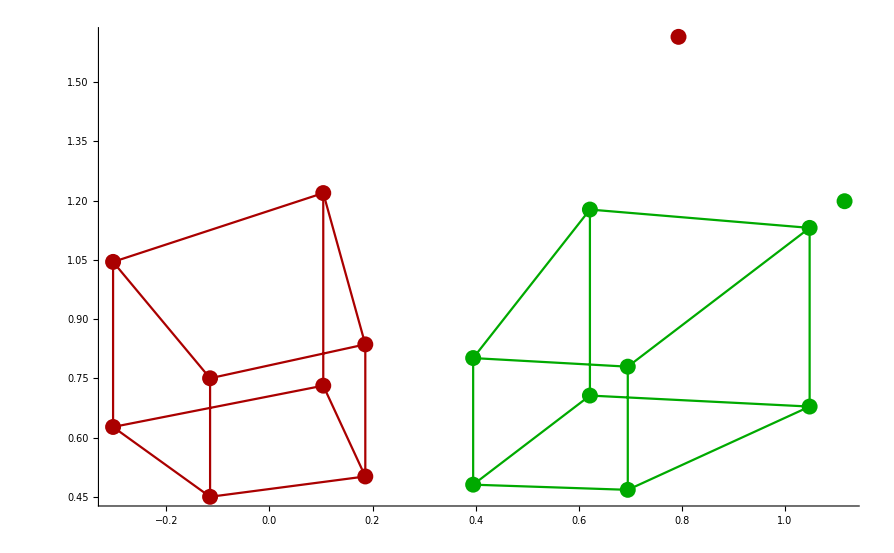

ImagePlaneC1Points = ((3 Cos[5 °]-4 Sin[5 °])/(4 Cos[5 °]+3 Sin[5 °]) | 3/(4 Cos[5 °]+3 Sin[5 °]) | 1
(5 Cos[5 °]-4 Sin[5 °])/(4 Cos[5 °]+5 Sin[5 °]) | 3/(4 Cos[5 °]+5 Sin[5 °]) | 1
(5 Cos[5 °]-4 Sin[5 °])/(4 Cos[5 °]+5 Sin[5 °]) | 5/(4 Cos[5 °]+5 Sin[5 °]) | 1
(3 Cos[5 °]-4 Sin[5 °])/(4 Cos[5 °]+3 Sin[5 °]) | 5/(4 Cos[5 °]+3 Sin[5 °]) | 1
(Cos[5 °]-2 Sin[5 °])/(2 Cos[5 °]+Sin[5 °]) | 1/(2 Cos[5 °]+Sin[5 °]) | 1
(5 Cos[5 °]-6 Sin[5 °])/(6 Cos[5 °]+5 Sin[5 °]) | 3/(6 Cos[5 °]+5 Sin[5 °]) | 1
(5 Cos[5 °]-6 Sin[5 °])/(6 Cos[5 °]+5 Sin[5 °]) | 5/(6 Cos[5 °]+5 Sin[5 °]) | 1
(Cos[5 °]-2 Sin[5 °])/(2 Cos[5 °]+Sin[5 °]) | 5/(3 (2 Cos[5 °]+Sin[5 °])) | 1
(4 Cos[5 °]-3 Sin[5 °])/(3 Cos[5 °]+4 Sin[5 °]) | 4/(3 Cos[5 °]+4 Sin[5 °]) | 1)

ImagePlaneC2Points = (-0.303249 | 0.626981 | 1.
0.104465 | 0.731566 | 1.
0.104465 | 1.21928 | 1.
-0.303249 | 1.04497 | 1.
-0.115086 | 0.450165 | 1.
0.186019 | 0.501657 | 1.
0.186019 | 0.836096 | 1.
-0.115086 | 0.750276 | 1.
0.793584 | 1.61482 | 1.)

CoefficientMtx = (-0.188535 | -0.214248 | -0.303249 | 0.389805 | 0.442966 | 0.626981 | 0.621716 | 0.706506 | 1.
0.10947 | 0.0708947 | 0.104465 | 0.766616 | 0.496476 | 0.731566 | 1.04791 | 0.678647 | 1.
0.10947 | 0.118158 | 0.104465 | 1.27769 | 1.3791 | 1.21928 | 1.04791 | 1.13108 | 1.
-0.188535 | -0.357079 | -0.303249 | 0.649674 | 1.23046 | 1.04497 | 0.621716 | 1.17751 | 1.
-0.0454845 | -0.0553418 | -0.115086 | 0.177916 | 0.216473 | 0.450165 | 0.395223 | 0.480874 | 1.
0.129314 | 0.0870205 | 0.186019 | 0.348733 | 0.234677 | 0.501657 | 0.695162 | 0.467804 | 1.
0.129314 | 0.145034 | 0.186019 | 0.581222 | 0.651881 | 0.836096 | 0.695162 | 0.779673 | 1.
-0.0454845 | -0.0922364 | -0.115086 | 0.296526 | 0.601314 | 0.750276 | 0.395223 | 0.801457 | 1.
0.885399 | 0.951195 | 0.793584 | 1.80165 | 1.93553 | 1.61482 | 1.1157 | 1.19861 | 1.)

MatrixRank[CoefficientMtx]8

ns ={{2.473×10^-16,-0.241845,-5.49814×10^-17,-0.0616284,-4.50525×10^-16,0.704416,-3.306×10^-16,-0.664463,-9.56025×10^-17}}

F = (2.473×10^-16 | -0.241845 | -5.49814×10^-17
-0.0616284 | -4.50525×10^-16 | 0.704416
-3.306×10^-16 | -0.664463 | -9.56025×10^-17)

lC1 = {{-0.170865,0.666101,-0.469447},{-0.164127,0.639835,-0.450936},{-0.273546,0.639835,-0.75156},{-0.284775,0.666101,-0.782412},{-0.116297,0.680059,-0.319523},{-0.113136,0.661574,-0.310838},{-0.18856,0.661574,-0.518064},{-0.193828,0.680059,-0.532539},{-0.289877,0.635657,-0.79643}}

lPrimeC1 = {{-0.0386399,-0.591124,0.441656},{-0.0450853,-0.689727,0.515327},{-0.0751421,-0.689727,0.858878},{-0.0643998,-0.591124,0.736093},{-0.027743,-0.63663,0.317104},{-0.0309164,-0.709451,0.353376},{-0.0515273,-0.709451,0.588959},{-0.0462383,-0.63663,0.528506},{-0.0995187,-0.856387,1.1375}}

e = {-0.996195,3.37292×10^-16,-0.0871557}

e' = {-0.939693,-9.20302×10^-17,0.34202}

EpipoleLines = (0.36397 | -1.4189 | 1.
0.36397 | -1.4189 | 1.
0.36397 | -0.851342 | 1.
0.36397 | -0.851342 | 1.
0.36397 | -2.12836 | 1.
0.36397 | -2.12836 | 1.
0.36397 | -1.27701 | 1.
0.36397 | -1.27701 | 1.
0.36397 | -0.798133 | 1.)

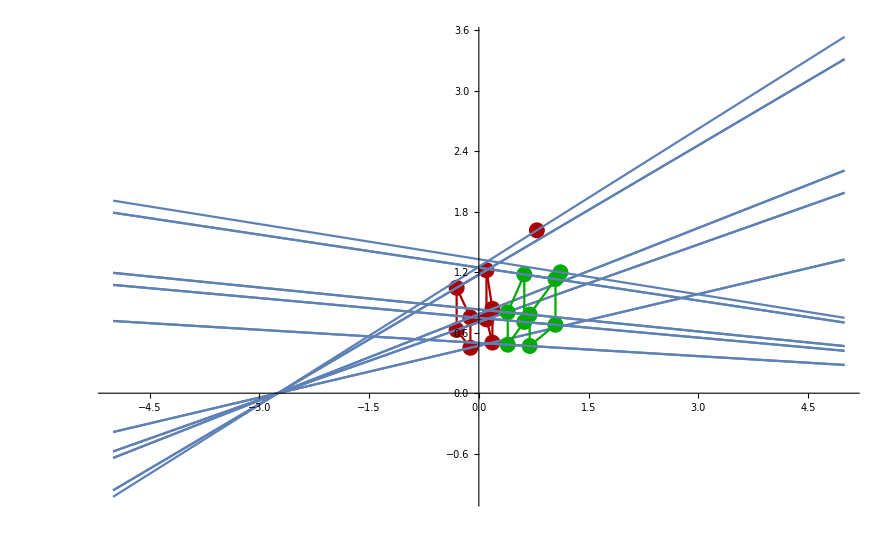

Begin Computing essential Matrix___________________________________________________

EMtx = (2.473×10^-16 | -0.241845 | 5.49814×10^-17
-0.0616284 | -4.50525×10^-16 | -0.704416
3.306×10^-16 | 0.664463 | -9.56025×10^-17)

U of E = {{0.,-0.34202,-0.939693},{-1.,1.37804×10^-16,-7.01571×10^-17},{6.66134×10^-16,0.939693,-0.34202}}

Sigma of E = {{0.707107,0.,0.},{0.,0.707107,0.},{0.,0.,0.}}

V of E = {{0.0871557,3.33067×10^-16,-0.996195},{3.18807×10^-16,1.,3.37292×10^-16},{0.996195,-3.50638×10^-16,0.0871557}}

S1 = (0. | 0.34202 | -2.27831×10^-16
-0.34202 | 0. | 0.939693
2.27831×10^-16 | -0.939693 | 0.)

S2 = (0. | -0.34202 | 2.27831×10^-16
0.34202 | 0. | -0.939693
-2.27831×10^-16 | 0.939693 | 0.)

R1 = (0.965926 | -2.07912×10^-16 | 0.258819
-2.75187×10^-16 | -1. | 2.07244×10^-16
0.258819 | 2.51193×10^-16 | -0.965926)

R2 = (0.906308 | -4.25989×10^-16 | -0.422618
4.14968×10^-16 | 1. | -2.19473×10^-16
0.422618 | -4.81914×10^-16 | 0.906308)

Test R1 is rotation ={{1.,1.39373×10^-16,-2.22045×10^-16},{1.39373×10^-16,1.,-5.03689×10^-16},{-2.22045×10^-16,-5.03689×10^-16,1.}}

Test R2 is rotation ={{1.,-1.74775×10^-16,1.11022×10^-16},{-1.74775×10^-16,1.,-4.76205×10^-16},{1.11022×10^-16,-4.76205×10^-16,1.}}

Check if t of S1, S2 is equal = {{{0.939693,2.22045×10^-16,0.34202}},{{0.939693,2.22045×10^-16,0.34202}}}

t = {0.939693,2.22045×10^-16,0.34202}

P21  = (0.906308 | -4.25989×10^-16 | -0.422618 | -0.939693
4.14968×10^-16 | 1. | -2.19473×10^-16 | -2.22045×10^-16
0.422618 | -4.81914×10^-16 | 0.906308 | -0.34202)

P22  = (0.965926 | -2.07912×10^-16 | 0.258819 | -0.939693
-2.75187×10^-16 | -1. | 2.07244×10^-16 | -2.22045×10^-16
0.258819 | 2.51193×10^-16 | -0.965926 | -0.34202)

P23  = (0.906308 | -4.25989×10^-16 | -0.422618 | 0.939693
4.14968×10^-16 | 1. | -2.19473×10^-16 | 2.22045×10^-16
0.422618 | -4.81914×10^-16 | 0.906308 | 0.34202)

P24  = (0.965926 | -2.07912×10^-16 | 0.258819 | 0.939693
-2.75187×10^-16 | -1. | 2.07244×10^-16 | 2.22045×10^-16
0.258819 | 2.51193×10^-16 | -0.965926 | 0.34202)

End Computing essential Matrix___________________________________________________

PList = {{{0.906308,-4.25989×10^-16,-0.422618,-0.939693},{4.14968×10^-16,1.,-2.19473×10^-16,-2.22045×10^-16},{0.422618,-4.81914×10^-16,0.906308,-0.34202}},{{0.965926,-2.07912×10^-16,0.258819,-0.939693},{-2.75187×10^-16,-1.,2.07244×10^-16,-2.22045×10^-16},{0.258819,2.51193×10^-16,-0.965926,-0.34202}},{{0.906308,-4.25989×10^-16,-0.422618,0.939693},{4.14968×10^-16,1.,-2.19473×10^-16,2.22045×10^-16},{0.422618,-4.81914×10^-16,0.906308,0.34202}},{{0.965926,-2.07912×10^-16,0.258819,0.939693},{-2.75187×10^-16,-1.,2.07244×10^-16,2.22045×10^-16},{0.258819,2.51193×10^-16,-0.965926,0.34202}}}

Length PList = 4

End Reconstruction of Rotation and Translation________________________________________________

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{0.439994,0.5,-0.707708},{0.772058,0.5,-0.73676},{0.772058,0.833333,-0.73676},{0.439994,0.833333,-0.707708},{0.410942,0.5,-1.03977},{0.743007,0.5,-1.06882},{0.743007,0.833333,-1.06882},{0.410942,0.833333,-1.03977},{1.2411,1.33333,-1.1124}}

ScaleValue = 6.81828

RForOk2 = {{0.906308,4.14968×10^-16,0.422618},{-4.25989×10^-16,1.,-4.81914×10^-16},{-0.422618,-2.19473×10^-16,0.906308}}

tForOK2 = {-0.939693,-2.22045×10^-16,-0.34202}

t = {0.996195,-3.43078×10^-16,-0.0871557}

Reconstructed scaled Points 3D = (3. | 3.40914 | -4.82535
5.26411 | 3.40914 | -5.02343
5.26411 | 5.6819 | -5.02343
3. | 5.6819 | -4.82535
2.80192 | 3.40914 | -7.08946
5.06603 | 3.40914 | -7.28755
5.06603 | 5.6819 | -7.28755
2.80192 | 5.6819 | -7.08946
8.4622 | 9.09104 | -7.58467)

-Graphics3D-

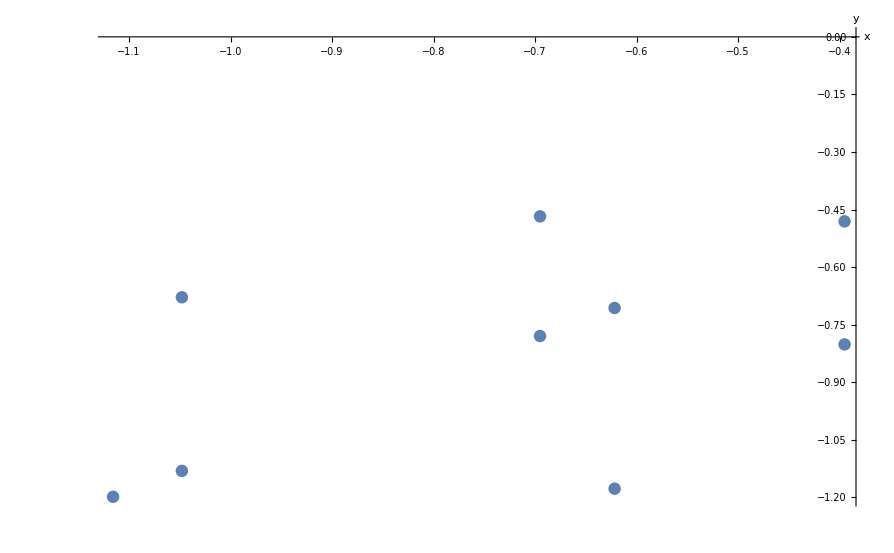

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-4.50579×10^14,-5.12029×10^14,7.24734×10^14},{1.15809,0.75,-1.10514},{1.15809,1.25,-1.10514},{-4.1747×10^14,-7.90674×10^14,6.71479×10^14},{-3.62813×10^14,-4.41441×10^14,9.17996×10^14},{1.11451,0.75,-1.60324},{1.11451,1.25,-1.60324},{-3.21793×10^14,-6.52552×10^14,8.14207×10^14},{0.744662,0.8,-0.667441}}

ScaleValue = -6.6581×10^-15

RForOk2 = {{0.965926,-2.75187×10^-16,0.258819},{-2.07912×10^-16,-1.,2.51193×10^-16},{0.258819,2.07244×10^-16,-0.965926}}

tForOK2 = {-0.939693,-2.22045×10^-16,-0.34202}

t = {0.996195,-3.31505×10^-16,-0.0871557}

Reconstructed scaled Points 3D = (3. | 3.40914 | -4.82535
-7.71066×10^-15 | -4.99357×10^-15 | 7.35812×10^-15
-7.71066×10^-15 | -8.32262×10^-15 | 7.35812×10^-15
2.77955 | 5.26438 | -4.47077
2.41564 | 2.93915 | -6.1121
-7.42051×10^-15 | -4.99357×10^-15 | 1.06745×10^-14
-7.42051×10^-15 | -8.32262×10^-15 | 1.06745×10^-14
2.14253 | 4.34475 | -5.42107
-4.95803×10^-15 | -5.32648×10^-15 | 4.44389×10^-15)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-0.439994,-0.5,0.707708},{-0.772058,-0.5,0.73676},{-0.772058,-0.833333,0.73676},{-0.439994,-0.833333,0.707708},{-0.410942,-0.5,1.03977},{-0.743007,-0.5,1.06882},{-0.743007,-0.833333,1.06882},{-0.410942,-0.833333,1.03977},{-1.2411,-1.33333,1.1124}}

ScaleValue = -6.81828

RForOk2 = {{0.906308,4.14968×10^-16,0.422618},{-4.25989×10^-16,1.,-4.81914×10^-16},{-0.422618,-2.19473×10^-16,0.906308}}

tForOK2 = {0.939693,2.22045×10^-16,0.34202}

t = {-0.996195,3.43078×10^-16,0.0871557}

Reconstructed scaled Points 3D = (3. | 3.40914 | -4.82535
5.26411 | 3.40914 | -5.02343
5.26411 | 5.6819 | -5.02343
3. | 5.6819 | -4.82535
2.80192 | 3.40914 | -7.08946
5.06603 | 3.40914 | -7.28755
5.06603 | 5.6819 | -7.28755
2.80192 | 5.6819 | -7.08946
8.4622 | 9.09104 | -7.58467)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{4.50579×10^14,5.12029×10^14,-7.24734×10^14},{-1.15809,-0.75,1.10514},{-1.15809,-1.25,1.10514},{4.1747×10^14,7.90674×10^14,-6.71479×10^14},{3.62813×10^14,4.41441×10^14,-9.17996×10^14},{-1.11451,-0.75,1.60324},{-1.11451,-1.25,1.60324},{3.21793×10^14,6.52552×10^14,-8.14207×10^14},{-0.744662,-0.8,0.667441}}

ScaleValue = 6.6581×10^-15

RForOk2 = {{0.965926,-2.75187×10^-16,0.258819},{-2.07912×10^-16,-1.,2.51193×10^-16},{0.258819,2.07244×10^-16,-0.965926}}

tForOK2 = {0.939693,2.22045×10^-16,0.34202}

t = {-0.996195,3.31505×10^-16,0.0871557}

Reconstructed scaled Points 3D = (3. | 3.40914 | -4.82535
-7.71066×10^-15 | -4.99357×10^-15 | 7.35812×10^-15
-7.71066×10^-15 | -8.32262×10^-15 | 7.35812×10^-15
2.77955 | 5.26438 | -4.47077
2.41564 | 2.93915 | -6.1121
-7.42051×10^-15 | -4.99357×10^-15 | 1.06745×10^-14
-7.42051×10^-15 | -8.32262×10^-15 | 1.06745×10^-14
2.14253 | 4.34475 | -5.42107
-4.95803×10^-15 | -5.32648×10^-15 | 4.44389×10^-15)

-Graphics3D-

-Graphics-

Begin New Rectification with Disortion minimization criterion_______________________________________________

pi = {{0.621716,0.706506,1.},{1.04791,0.678647,1.},{1.04791,1.13108,1.},{0.621716,1.17751,1.},{0.395223,0.480874,1.},{0.695162,0.467804,1.},{0.695162,0.779673,1.},{0.395223,0.801457,1.},{1.1157,1.19861,1.}}

pj = {{-0.303249,0.626981,1.},{0.104465,0.731566,1.},{0.104465,1.21928,1.},{-0.303249,1.04497,1.},{-0.115086,0.450165,1.},{0.186019,0.501657,1.},{0.186019,0.836096,1.},{-0.115086,0.750276,1.},{0.793584,1.61482,1.}}

n = 9

minXpi = 0.395223

maxXPi = 1.1157

minYpi = 0.467804

maxYPi = 1.19861

minXPj = -0.303249

maxXPj = 0.793584

minYPj = 0.450165

maxYPj = 1.61482

piWidth = 2.

piHeight = 2.

pjWidth = 2.

pjHeight = 2.

pc = (0.737302
0.824684
1.)

pcPrime = (0.0597646
0.863979
1.)

P = {{-0.115586,0.310609,0.310609,-0.115586,-0.34208,-0.0421401,-0.0421401,-0.34208,0.378395},{-0.118178,-0.146037,0.306395,0.352826,-0.34381,-0.356881,-0.0450115,-0.023227,0.373923},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PPrime = {{-0.363014,0.0447001,0.0447001,-0.363014,-0.17485,0.126255,0.126255,-0.17485,0.733819},{-0.236997,-0.132412,0.355298,0.18099,-0.413813,-0.362321,-0.0278828,-0.113703,0.75084},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PP = {{0.600447,0.306668,0.},{0.306668,0.64161,0.},{0.,0.,0.}}

PPPrime = {{0.899071,0.624247,0.},{0.624247,1.11268,0.},{0.,0.,0.}}

pc = {0.737302,0.824684,1.}

pcpc = {{0.543615,0.608042,0.737302},{0.608042,0.680104,0.824684},{0.737302,0.824684,1.}}

pcpcPrime = {{0.00357181,0.0516353,0.0597646},{0.0516353,0.746459,0.863979},{0.0597646,0.863979,1.}}

A = (0.00487375 | -0.00232949 | -0.0557072
-0.00232949 | 0.00456107 | 0.0266262
-0.0557072 | 0.0266262 | 0.636736)

B = (0.00258308 | 0.0428332 | -0.0295247
0.0428332 | 0.710271 | -0.489586
-0.0295247 | -0.489586 | 0.337469)

APrime = (0.130159 | -0.073023 | 0.357609
-0.073023 | 0.105171 | -0.200629
0.357609 | -0.200629 | 0.982521)

BPrime = (-7.8696×10^-19 | 0.00250058 | -1.20248×10^-17
0.0111256 | 2.64264×10^-16 | -0.349386
2.92752×10^-18 | -0.47824 | -5.81837×10^-17)

{A[[1,1;;2]],A[[2,1;;2]]}={{0.00487375,-0.00232949},{-0.00232949,0.00456107}}

{APrime[[1,1;;2]],APrime[[2,1;;2]]}={{0.130159,-0.073023},{-0.073023,0.105171}}

DD ={{0.0698122,-0.033368},{0.,0.0587167}}

DDPrime ={{0.360775,-0.202406},{0.,0.253384}}

{B[[1,1;;2]],B[[2,1;;2]]}={{0.00258308,0.0428332},{0.0428332,0.710271}}

{BPrime[[1,1;;2]],BPrime[[2,1;;2]]}={{-7.8696×10^-19,0.00250058},{0.0111256,2.64264×10^-16}}

DTBD[[2,1]] = {0.04924,0.998787}

Eigensystem DTB1 = {{218.594,0.},{{0.04924,0.998787},{-0.998787,0.04924}}}

Eigensystem DTBPrimeD = {{0.142442,-0.023372},{{-0.188592,-0.982056},{-0.76028,0.649596}}}

z1 first = {8.83568,17.0103}

z1= {8.83568,17.0103}

z2 first = {-2.69716,-3.87577}

z2= {-2.69716,-3.87577}

z ={23.8901,23.8901,0.}

w = {2.08216,-2.08216,-23.7992}

wPrime = {-5.77769,-1.47231,-15.8741}

wPrime = {0.36397,0.0927492,1.}

w = {-0.0874887,0.0874887,1.}

HpPrime = (1. | 0. | 0.
0. | 1. | 0.
0.36397 | 0.0927492 | 1.)

Hp = (1. | 0. | 0.
0. | 1. | 0.
-0.0874887 | 0.0874887 | 1.)

ePrime inf = {-0.939693,-9.20302×10^-17,4.996×10^-16}

e inf = {-0.996195,3.37292×10^-16,0.}

HrPrime = (-0.704416 | -2.01849×10^-17 | 0.
2.01849×10^-17 | -0.704416 | 1.
0. | 0. | 1.)

Hr = (-0.664463 | 3.38964×10^-16 | 0.
-3.38964×10^-16 | -0.664463 | 1.
0. | 0. | 1.)

ePrimeHorizontal = {0.661935,5.4546×10^-16,4.996×10^-16}

eHorizontal = {0.661935,1.13557×10^-16,0.}

piA = {-0.72817,1.,1.}

piB = {-1.45634,0.27183,1.}

piC = {-0.611007,-0.222014,1.}

piD = {3.11695×10^-16,0.388993,1.}

piX = {-1.45634,-0.117163,0.}

piY = {0.117163,-1.22201,0.}

piSA = -0.840331

piSB = 0.0153085

{-0.704416,1.36397,1.36397}

pjA = {-0.516445,1.,1.}

pjB = {-0.77379,0.613105,1.}

pjC = {-0.454618,0.0907644,1.}

pjD = {-1.84717×10^-17,0.355373,1.}

pjX = {-0.77379,0.257732,0.}

pjY = {0.0618275,-0.909236,0.}

pjSA = -1.29887

pjSB = -0.371783

RecPointsC1 =(0.352766 | 0.534009 | 1.
0.61283 | 0.534009 | 1.
0.584781 | 0.253869 | 1.
0.334936 | 0.253869 | 1.
0.229492 | 0.682853 | 1.
0.406488 | 0.682853 | 1.
0.392744 | 0.485739 | 1.
0.220542 | 0.485739 | 1.)

RecPointsC2 =(-0.491281 | 0.534009 | 1.
-0.112106 | 0.534009 | 1.
-0.0113514 | 0.253869 | 1.
-0.375625 | 0.253869 | 1.
-0.359185 | 0.682853 | 1.
-0.101124 | 0.682853 | 1.
-0.0319777 | 0.485739 | 1.
-0.283049 | 0.485739 | 1.)

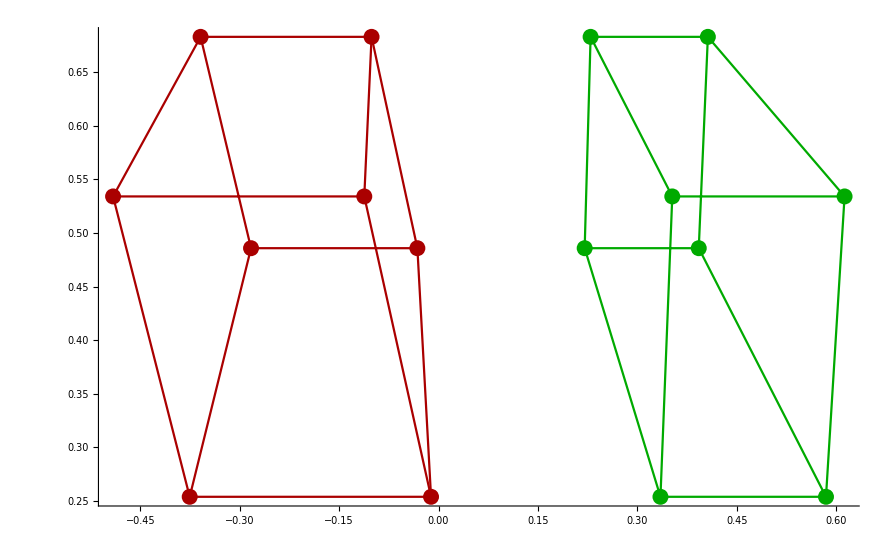

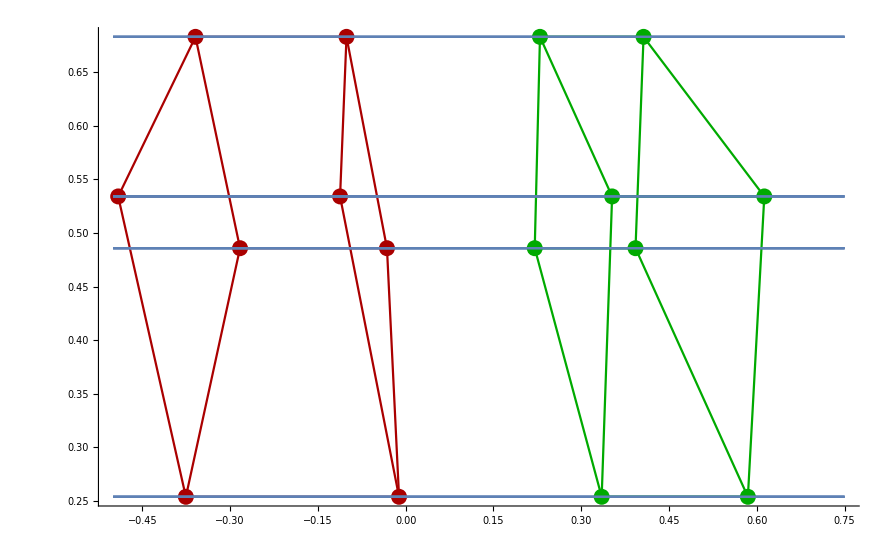

End New Rectification with Disortion minimization criterion_______________________________________________

```mathematica
StartComputation[];
```